Fit parameters = {ω1→0.598766,ce→0.000216863,cf→0.000216863,a→1.30709,b→0.270176,w→0.000294762}

r^2 = 0.999937

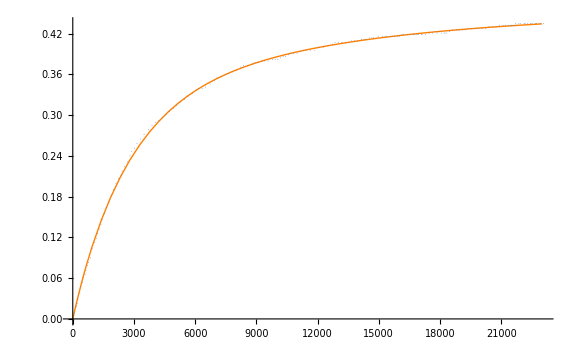

```mathematica
(* A thermal mixing model with more parameters *)
ClearAll["Global`*"];
(* Parameters to change:
 Below, you can change the value of the rates a and b.
* peInit, pfInit, and pnInit are the initial polarizations of the two types of electrons and the nuclei, respectively.
* ce and cf are the ratios of the number of each type of electron to the number of nuclei (the analogue to the constant C in the solid effect).
*)
(* Description of rate parameters:
Spin up/down is indicated by + or -; the states listed give the spins of electrons e, electrons f, and nuclei (in that order).
Pumping parameters are represented by ↔, while relaxation rates are represented by ->.
* a: +-+ ↔ -+-
* b: +-- ↔ -++
* q: --+ -> --- and +++ -> ++- (probably either useless or non-physical)
* r: +++ -> --+ and ++- -> --- (does not yield physical results)
* u: +-+ -> -+- and +-- -> -++ (similar to σ in Jeffries)
* v: +-+ -> -++ and +-- -> -+- (set this equal to 1, probably)
* w: +-+ -> +-- and -++ -> -+- (similar to θ in Jeffries)
*)
subs={nt->np[t]+nm[t],et->ep[t]+em[t],ft->fp[t]+fm[t]};
assumptions={v->1,q->0,r->0,u->0};
rates={ω1->0.005,a->5,b->1,w->1};
allRates=assumptions∪rates;
initial={peInit->-1,pfInit->1,pnInit->0};
constants={pe0->-1,pf0->0,pn0->0};
totalTime=5000;
epDot=cf/(ft nt)(-ep[t]fp[t]np[t](r(1-pe0-pf0))
-ep[t]fp[t]nm[t](r(1-pe0-pf0))
-ep[t] fm[t]np[t](a+u(1-pe0+pf0-pn0)+v(1-pe0+pf0))
-ep[t]fm[t]nm[t](b+u(1-pe0+pf0+pn0)+v(1-pe0+pf0))
+em[t] fp[t]np[t](b+u(1+pe0-pf0-pn0)+v(1+pe0-pf0))
+em[t] fp[t]nm[t](a+u(1+pe0-pf0)+v(1+pe0-pf0))
+em[t]fm[t]np[t](r(1+pe0+pf0))
+em[t]fm[t]nm[t](r(1+pe0+pf0)))ω1;
emDot=-epDot;
fpDot=ce/(et nt)(-fp[t]ep[t]np[t](r(1-pe0-pf0))
-fp[t]ep[t]nm[t](r(1-pe0-pf0))
-fp[t] em[t]np[t](b+u(1+pe0-pf0-pn0)+v(1+pe0-pf0))
-fp[t] em[t]nm[t](a+u(1+pe0-pf0+pn0)+v(1+pe0-pf0))
+fm[t] ep[t]np[t](a+u(1-pe0+pf0-pn0)+v(1-pe0+pf0))
+fm[t]ep[t]nm[t](b+u(1-pe0+pf0+pn0)+v(1-pe0+pf0))
+fm[t]em[t]np[t](r(1+pe0+pf0))
+fm[t]em[t]nm[t](r(1+pe0+pf0)))ω1;
fmDot=-fpDot;
npDot=ce/(et ft)(-np[t]ep[t]fp[t](q(1-pn0))
-np[t]ep[t]fm[t](a+u(1-pe0+pf0-pn0)+w(1-pn0))
-np[t]em[t]fp[t](b+u(1+pe0-pf0-pn0)+w(1-pn0))
-np[t]em[t]fm[t](q(1-pn0))
+nm[t]ep[t]fp[t](q(1+pn0))
+nm[t]ep[t]fm[t](b+u(1-pe0+pf0+pn0)+w(1+pn0))
+nm[t]em[t]fp[t](a+u(1+pe0-pf0+pn0)+w(1+pn0))
+nm[t]em[t]fm[t](q(1+pn0)))ω1;
nmDot=-npDot;
(* Get expressions for Subscript[P, n], etc. by defining them and eliminating np, nm, etc. *)
peExpr=(ep[t]-em[t])/et/.subs;
pfExpr=(fp[t]-fm[t])/ft/.subs;
pnExpr=(np[t]-nm[t])/nt/.subs;
fnSubs={pn->pn[t],pe->pe[t],pf->pf[t]};
pnDotEqn=pnDot/.Solve[Eliminate[{pnDot==(npDot-nmDot)/nt/.subs,
pn==pnExpr,pe==peExpr,pf==pfExpr},
{np[t],nm[t],ep[t],em[t],fp[t],fm[t]}],pnDot][[1]]/.fnSubs;
peDotEqn=peDot/.Solve[Eliminate[{peDot==(epDot-emDot)/et/.subs,
pn==pnExpr,pe==peExpr,pf==pfExpr},
{np[t],nm[t],ep[t],em[t],fp[t],fm[t]}],peDot][[1]]/.fnSubs;
pfDotEqn=pfDot/.Solve[Eliminate[{pfDot==(fpDot-fmDot)/ft/.subs,
pn==pnExpr,pe==peExpr,pf==pfExpr},
{np[t],nm[t],ep[t],em[t],fp[t],fm[t]}],pfDot][[1]]/.fnSubs;
eqns={pe'[t]==peDotEqn,pf'[t]==pfDotEqn,pn'[t]==pnDotEqn,pe[0]==peInit,pf[0]==pfInit,pn[0]==pnInit}/.initial;
sol=ParametricNDSolve[eqns/.assumptions/.constants,{pn,pe,pf},{t,0,25000},{ω1,ce,cf,a,b,w}];
data=Import["realdata.csv"];
(*bestFit=FindFit[data,{pn[ω1,ce,cf,a,b,w][t]/.sol,{0≤ω1≤100,0.5*^-4≤ce≤10*^-4,cf==ce,0≤a≤7,0≤b≤7,0≤w≤10}},{ω1,ce,cf,a,b,w},t]
Show[Plot[pn[ω1,ce,cf,a,b,w][t]/.bestFit/.sol,{t,0,23000},PlotStyle->{{Orange,Thick}}],ListPlot[data,PlotStyle->PointSize[0.001]],
ImageSize->Large,PlotRange->All]*)
Off[NonlinearModelFit::cvmit]
model=NonlinearModelFit[data,{pn[ω1,ce,cf,a,b,w][t]/.sol,0≤ω1≤100,0.5*^-4≤ce≤10*^-4,cf==ce,0≤a≤7,0≤b≤7,0≤w≤10},{ω1,ce,cf,a,b,w},t];
Print["Fit parameters = ",model["BestFitParameters"]]
Print["r^2 = ",model["AdjustedRSquared"]]
plot=Show[Plot[model[t],{t,0,23000},PlotStyle->{{Orange,Thick}}],ListPlot[data,PlotStyle->PointSize[0.001]],
ImageSize->Large,PlotRange->All]
```

```mathematica
data
```

{{86.262,0.00897577},{172.524,0.0179515},{215.655,0.0224394},{258.786,0.0291695},{345.048,0.0381452},{388.179,0.0471174},{474.441,0.0538511},{517.572,0.0605811},{603.834,0.0650726},{646.965,0.0718026},{733.227,0.0785362},{776.358,0.0830241},{862.62,0.0897577},{948.882,0.103218},{1078.27,0.112197},{1164.54,0.118931},{1207.67,0.125661},{1293.93,0.132394},{1380.19,0.139128},{1466.45,0.145862},{1552.72,0.154837},{1638.98,0.163813},{1768.37,0.172793},{1897.76,0.181772},{1984.03,0.190748},{2113.42,0.199727},{2242.81,0.206464},{2415.34,0.217689},{2372.2,0.210959},{2544.73,0.224427},{2674.12,0.231164},{2803.51,0.240143},{2889.78,0.246877},{3019.17,0.251372},{3148.56,0.258109},{3321.09,0.26485},{3493.61,0.271591},{3709.27,0.278335},{3881.79,0.285076},{4054.31,0.289574},{4226.84,0.291831},{4399.36,0.296329},{4571.88,0.300828},{4744.41,0.305327},{4916.93,0.309825},{5089.46,0.314324},{5261.98,0.318823},{5477.64,0.323325},{5650.16,0.327823},{5865.81,0.332326},{6038.34,0.336824},{6340.26,0.339092},{6167.73,0.339077},{6512.78,0.341348},{6728.43,0.34585},{6944.09,0.350352},{7073.48,0.354847},{7246.01,0.357104},{7504.79,0.359368},{7634.19,0.361621},{7806.71,0.363877},{8022.36,0.366137},{8238.02,0.370639},{8367.41,0.372892},{8583.07,0.37291},{8798.72,0.37517},{9100.64,0.377437},{8928.12,0.377423},{9273.16,0.379694},{9402.56,0.379705},{9575.08,0.379719},{9790.73,0.381979},{9920.13,0.38199},{10049.5,0.382},{10178.9,0.384253},{10308.3,0.386506},{10437.7,0.386517},{10567.1,0.38877},{10696.5,0.391023},{10825.9,0.391034},{10998.4,0.391048},{11170.9,0.393304},{11300.3,0.395557},{11429.7,0.395568},{11645.4,0.395586},{11861.,0.395604},{12076.7,0.400106},{12292.3,0.400124},{12508.,0.402384},{12723.6,0.404644},{12853.,0.406897},{13025.6,0.406911},{13198.1,0.406926},{13370.6,0.40694},{13543.1,0.406954},{13801.9,0.409218},{13974.4,0.409232},{14147.,0.411489},{14362.6,0.411507},{14535.1,0.413763},{14750.8,0.413781},{13672.5,0.409207},{14276.4,0.411499},{14664.5,0.413774},{14966.5,0.416041},{15182.1,0.416059},{15397.8,0.416077},{15570.3,0.416091},{15785.9,0.416109},{16001.6,0.416127},{16217.3,0.418387},{15311.5,0.41607},{15699.7,0.416102},{15915.3,0.41612},{16389.8,0.418401},{16131.,0.41838},{16562.3,0.418416},{16734.8,0.41843},{16950.5,0.418448},{17123.,0.418462},{17295.5,0.418477},{17468.1,0.420733},{17640.6,0.420747},{17856.2,0.420765},{18071.9,0.420783},{18244.4,0.420798},{18460.1,0.423058},{18632.6,0.425314},{18805.1,0.425328},{18934.5,0.425339},{19107.,0.425354},{19236.4,0.425364},{16691.7,0.418426},{16864.2,0.418441},{17079.9,0.418459},{17770.,0.423},{19365.8,0.427617},{19538.3,0.427631},{19710.9,0.427646},{19883.4,0.42766},{20055.9,0.427674},{20228.4,0.427689},{20401.,0.429945},{20573.5,0.42996},{20746.,0.429974},{20918.5,0.43223},{21091.1,0.432245},{21220.4,0.432255},{21349.8,0.432266},{21479.2,0.432277},{21608.6,0.432288},{21738.,0.432298},{21953.7,0.434559},{21867.4,0.434551},{21694.9,0.434537},{21522.4,0.432281},{22169.3,0.434576},{22126.2,0.434573},{22298.7,0.434587},{22428.1,0.434598},{22514.4,0.434605},{18201.3,0.420794},{17942.5,0.423015},{18330.7,0.420805},{22730.,0.434623},{22902.6,0.434637},{23075.1,0.434652},{22686.9,0.434619}}